```mathematica
λ=633*10^(-9);
```

```mathematica
d=0.12*10^(-3);
```

```mathematica
f[x_]:=(Sin[(Pi*d/λ)*Sin[x]]/((Pi*d/λ)*Sin[x]))^2
```

```mathematica
P=Plot[f[x],{x,-0.013,0.013},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},Frame->True,FrameLabel->{Style["α / rad",Bold,16],Style["I/I(0)",Bold,16]},ScalingFunctions->{Automatic},PlotLegends->{"Rendija d=0.12 mm"}];
```

```mathematica
F=ListPlot[{{0.0062,0.2275},{-0.00647,0.25},{0,1}},PlotStyle->{Black,Thickness[0.003]},PlotLegends->{"Datos rendija d=0.12 mm"}];
```

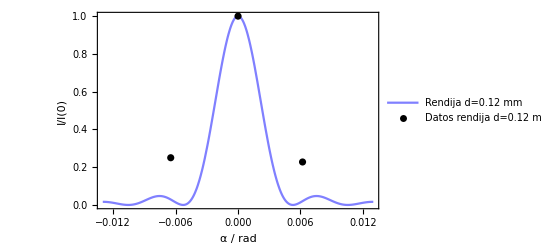

```mathematica
Show[P,F]
```